# Pedagogical walk-through of the HiddenRegionFinder algorithm

Steps in Hidden Region Finder Algorithm:  
factor discovery, 
admissibility checks, 
generator products, 
obstruction extraction by polynomial division, 
scaling-constraint diagnostics.

## Setup

```mathematica
ClearAll["Global`*"];
Get[NotebookDirectory[]<>"HiddenRegionFinder.wl"];
$HRFScalingReport = False;
```

```mathematica
Get[NotebookDirectory[]<>"03_FivePoint_Spacelike_Collinear.wl"];
```

scaling interior 7-prop graph 1/6

scaling interior 7-prop graph 2/6

coverage scaling: accepted=104/279935 selected={-2,-1,-2,-2,-2,-1,-2} wFSL=-5 wLP=-4 gap=1 missing={}

scaling interior 7-prop graph 3/6

scaling interior 7-prop graph 4/6

scaling interior 7-prop graph 5/6

coverage scaling: accepted=109/279935 selected={-2,-1,-2,-2,-2,-1,0} wFSL=-5 wLP=-4 gap=1 missing={}

scaling interior 7-prop graph 6/6

scaling interior 8-prop graph 1/9

scaling interior 8-prop graph 2/9

scaling interior 8-prop graph 3/9

scaling interior 8-prop graph 4/9

scaling interior 8-prop graph 5/9

scaling interior 8-prop graph 6/9

scaling interior 8-prop graph 7/9

scaling interior 8-prop graph 8/9

scaling interior 8-prop graph 9/9

scaling boundary 7-prop case 1/6

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 7-prop case 2/6

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 7-prop case 3/6

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 7-prop case 4/6

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 7-prop case 5/6

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 7-prop case 6/6

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 8-prop case 1/12

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 8-prop case 2/12

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 8-prop case 3/12

coverage scaling: accepted=104/279935 selected={-2,-1,-2,-2,-2,-1,-2} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 8-prop case 4/12

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 8-prop case 5/12

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 8-prop case 6/12

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 8-prop case 7/12

coverage scaling: accepted=104/279935 selected={-2,-1,-2,-2,-2,-1,-2} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 8-prop case 8/12

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 8-prop case 9/12

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 8-prop case 10/12

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 8-prop case 11/12

coverage scaling: accepted=104/279935 selected={-2,-1,-2,-2,-2,-1,-2} wFSL=-5 wLP=-4 gap=1 missing={}

scaling boundary 8-prop case 12/12

coverage scaling: accepted=100/46655 selected={-2,-1,-2,-2,-2,-1} wFSL=-5 wLP=-4 gap=1 missing={}

## Layer I: From a graph to U, F, and P

The graph input follows the pySecDec convention used throughout the package. Internal lines are labelled by masses and endpoint vertices. External lines are labelled by momenta and the vertex to which they attach.

{{0,{1,3}},{0,{1,5}},{0,{2,3}},{0,{2,5}},{0,{3,4}},{0,{4,5}}}

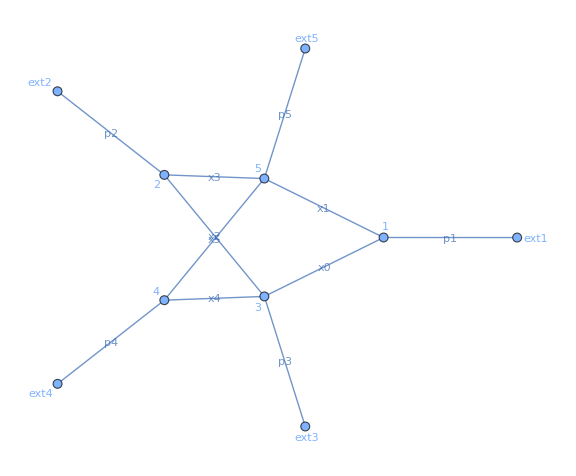

```mathematica
seedInternalLines = {
  {"0", {1, 3}}, {"0", {1, 5}}, {"0", {2, 3}},
  {"0", {2, 5}}, {"0", {3, 4}}, {"0", {4, 5}}
}
seedExternalLines = { {p1, 1}, {p2, 2}, {p3, 3}, {p4, 4}, {p5, 5}};

drawGraphFromPySecDecInput[seedInternalLines, seedExternalLines]
```

```mathematica
Clear[{Useed,Fseed}]
```

```mathematica
{Useed,Fseed}=toCyclicMandelstams[{"U","F"}/.SymanzikUF[seedInternalLines, seedExternalLines]];
Pseed = Expand[Useed + Fseed];
<|"U" -> Useed, "F" -> Fseed, "P" -> Pseed|>
```

<|U→x0 x2+x1 x2+x0 x3+x1 x3+x0 x4+x1 x4+x2 x4+x3 x4+x0 x5+x1 x5+x2 x5+x3 x5,F→-s12 x1 x2 x4-s23 x1 x2 x4+s45 x1 x2 x4+s23 x0 x3 x4+s45 x1 x3 x4+s34 x0 x2 x5-s12 x1 x2 x5-s15 x1 x2 x5+s34 x1 x2 x5+s15 x0 x3 x5,P→x0 x2+x1 x2+x0 x3+x1 x3+x0 x4+x1 x4+x2 x4-s12 x1 x2 x4-s23 x1 x2 x4+s45 x1 x2 x4+x3 x4+s23 x0 x3 x4+s45 x1 x3 x4+x0 x5+x1 x5+x2 x5+s34 x0 x2 x5-s12 x1 x2 x5-s15 x1 x2 x5+s34 x1 x2 x5+x3 x5+s15 x0 x3 x5|>

## Layer II: Cancellation factors f_i

The LaTeX notes define cancellation factors as non-monomial factors appearing in derivatives of the strict leading polynomial F0, or, in the extended version, in coefficients of independent kinematic structures inside those derivatives. The package implements this distinction by derivativeFactors and derivativeFactorsExtended.

Toy example: use a simple polynomial whose derivative with respect to x4 contains two binomial factors. This is not a physical graph; it is only a transparent algebraic test of the factor/generator/obstruction machinery.

```mathematica
toyVars = {x0, x1, x2, x3, x4};
toyKinVars = {};
toyKinAssumptions = True;
toyF0 = Expand[x4 (x0 - x1) (x2 - x3) + x0 x2];

<|
  "F0" -> toyF0,
  "DerivativeFactors" -> derivativeFactors[toyF0, toyVars],
  "SafeCancellationFactors" -> safeCancellationFactors[toyF0, toyVars, toyKinAssumptions, toyKinVars][[1]]
|>
```

The package keeps only binomial factors that pass positiveCompatibleQ. Internally this uses Reduce with x_e>0 and the chosen kinematic assumptions.

```mathematica
factorData = safeCancellationFactors[toyF0, toyVars, toyKinAssumptions, toyKinVars];
toySafeFactors = factorData[[1]];
AssociationThread[toySafeFactors, positiveCompatibleQ[#, toyVars, toyKinAssumptions, toyKinVars] & /@ toySafeFactors]
```

Important implementation audit: the current production routine tests individual factors for positivity. The stricter simultaneous-admissibility condition for a subset S is included here as an audit helper, but it is not currently used as a hard gate in findObstructions.

```mathematica
ClearAll[hrfAdmissibleSubsetQ];
hrfAdmissibleSubsetQ[S_, vars_, kinAssumptions_, kinVars_] := Reduce[
  kinAssumptions && And @@ Thread[vars > 0] && And @@ Thread[S == 0],
  Join[vars, kinVars], Reals
] =!= False;

Subsets[toySafeFactors, {1, Length[toySafeFactors]}] /. S_List :> <|"Subset" -> S, "SimultaneouslyAdmissibleQ" -> hrfAdmissibleSubsetQ[S, toyVars, toyKinAssumptions, toyKinVars]|>
```

## Layer III: Generator products g_k and the cancellation ideal

The generators of the cancellation ideal are not the individual factors f_i. They are products of factors, g_k=Product[f_i, {i in S_k}], as in the current LaTeX notes. The package can use a single full product or scan pair-sector products.

```mathematica
<|
  "SafeFactors" -> toySafeFactors,
  "PairSectorGenerators" -> pairSectorGenerators[toySafeFactors],
  "CandidateGeneratorSets_SingleProduct" -> candidateGeneratorSets[toySafeFactors],
  "CandidateGeneratorSets_Diagnostic" -> candidateGeneratorSetsDiagnostic[toySafeFactors, 2]
|>
```

## Layer IV: Obstruction as a remainder after division by generator products

For a chosen generator set G, obstructionByOriginalTermsGeneral searches for a subset of original monomials of F0 whose removal makes the remainder lie in the ideal <G>. The implementation introduces binary variables b_i selecting obstruction monomials and computes PolynomialReduce[F0 - Sum[b_i m_i], G, allVars][[2]]. It then imposes that all coefficients of this remainder vanish, with b_i in {0,1}.

```mathematica
toyGenerators = {Times @@ toySafeFactors};
toyObs = obstructionByOriginalTermsGeneral[toyF0, toyGenerators, toyVars, toyKinVars, 8];
toyUse = generatorUseData[toyObs["Superleading"], toyGenerators, toyVars, toyKinVars];
<|
  "Generators" -> toyGenerators,
  "ObstructionTerms" -> toyObs["ObstructionTerms"],
  "F_Obs" -> toyObs["Obstruction"],
  "F_SL" -> toyObs["Superleading"],
  "PolynomialReduceQuotients" -> toyUse["Quotients"],
  "PolynomialReduceRemainder" -> toyUse["Remainder"],
  "UsedGenerators" -> toyUse["UsedGenerators"]
|>
```

```mathematica
(* Full diagnostic scan over generator-set candidates. *)
obstructionGeneratorDiagnostic[toyF0, toyVars, toyKinAssumptions, toyKinVars, 8, 2]
```

## Project command pattern for the five-point collinear example

After running 03_FivePoint_Spacelike_Collinear.wl, the same objects are available for actual graph topologies. The following cells are written defensively: they only run if the example data already exist in the kernel.

```mathematica
If[ValueQ[UFCollinear2Loop7Prop],
  case7 = First@Select[UFCollinear2Loop7Prop, AssociationQ[Lookup[# ["InteriorObstructionScan"], "ObstructionData", Missing[]]] &];
  obs7 = case7["InteriorObstructionScan", "ObstructionData"];
  <|
    "Topology" -> case7["TopologyTeX"],
    "CancellationFactors" -> case7["InteriorObstructionScan", "CancellationFactors"],
    "Generators" -> case7["InteriorObstructionScan", "Generators"],
    "F_Obs" -> obs7["Obstruction"],
    "F_SL" -> obs7["Superleading"],
    "GeneratorUseData" -> case7["InteriorObstructionScan", "GeneratorUseData"]
  |>,
  "Run Get[NotebookDirectory[]<>\"03_FivePoint_Spacelike_Collinear.wl\"] first to use this cell."
]
```

## Layer V: Scaling geometry and uniqueness diagnostics

The scaling routine enforces three conditions: (1) all F_SL monomials have one common pre-cancellation weight W_SL; (2) W_SL is strictly more singular than the first surviving Lee--Pomeransky weight W_HR from U+F_Obs; (3) every active variable is covered either by an F_SL monomial at W_SL or by a surviving U/F_Obs monomial at W_HR. The unit gap is reported but not imposed.

```mathematica
ClearAll[hrfFSLLinearConstraintData];
hrfFSLLinearConstraintData[fSL_, vars_] := Module[{fSLList, rows, A},
  fSLList = DeleteCases[Flatten[{fSL}], 0];
  rows = Join @@ (polynomialExponentRows[#, vars] & /@ fSLList);
  If[Length[rows] < 2, Return[<|"ExponentRows" -> rows, "ConstraintMatrix" -> {}, "Rank" -> 0, "NullSpace" -> IdentityMatrix[Length[vars]], "AffineDimensionIgnoringDeltaPowers" -> Length[vars]|>]];
  A = Rest[rows] - ConstantArray[First[rows], Length[rows] - 1];
  <|
    "ExponentRows" -> rows,
    "ConstraintMatrix" -> A,
    "Rank" -> MatrixRank[A],
    "NullSpace" -> NullSpace[A],
    "AffineDimensionIgnoringDeltaPowers" -> Length[vars] - MatrixRank[A]
  |>
];
```

```mathematica
ClearAll[hrfScalingGeometryAudit];
hrfScalingGeometryAudit[fSL_, U_, vars_, maxAbs_:5, fObs_:None] := Module[{lin, scan, accepted},
  lin = hrfFSLLinearConstraintData[fSL, vars];
  scan = findCoverageLPScaling[fSL, U, vars, maxAbs, fObs];
  accepted = Lookup[scan, "AcceptedCandidateDiagnostics", {}];
  <|
    "LinearEqualityData" -> lin,
    "SelectedScaling" -> Lookup[scan, "Scaling", Missing["NoScaling"]],
    "AcceptedCount" -> Lookup[scan, "AcceptedCount", Missing["NoCount"]],
    "CandidateCount" -> Lookup[scan, "CandidateCount", Missing["NoCount"]],
    "AcceptedScalings" -> Lookup[#, "ScalingVector"] & /@ accepted,
    "SelectedDiagnostics" -> If[accepted === {}, Missing["NoAcceptedCandidate"], First[accepted]],
    "NearMissDiagnostics" -> Lookup[scan, "NearMissDiagnostics", {}]
  |>
];
```

Apply the scaling audit to the toy obstruction. For the toy example we choose a simple toy U only to demonstrate the diagnostic structure; physical conclusions should be drawn from the graph examples below.

```mathematica
toyU = x0 + x1 + x2 + x3 + x4;
hrfScalingGeometryAudit[toyObs["Superleading"], toyU, toyVars, 3, toyObs["Obstruction"]]
```

Apply the scaling audit to a real five-point collinear topology, if 03 has been loaded.

```mathematica
If[ValueQ[case7] && AssociationQ[case7],
  hrfScalingGeometryAudit[obs7["Superleading"], case7["U"], case7["Variables"], 5, obs7["Obstruction"]],
  "Load 03_FivePoint_Spacelike_Collinear.wl and run the previous project-data cell first."
]
```

### Compact accepted-candidate table

```mathematica
ClearAll[hrfAcceptedCandidateTable];
hrfAcceptedCandidateTable[scan_Association] := Dataset[
  KeyTake[#, {
    "ScalingVector", "FSLWeight", "PostCancellationLeadingWeight",
    "HierarchyGapPostLPminusFSL", "UnitGapQ",
    "VariablesCoveredByFSLAtWSL", "VariablesInPostCancellationLeadingSupport",
    "VariablesMissingFromLeadingRegionCoverage"
  }] & /@ Lookup[scan, "AcceptedCandidateDiagnostics", {}]
];

If[ValueQ[case7] && AssociationQ[case7],
  hrfAcceptedCandidateTable[findCoverageLPScaling[obs7["Superleading"], case7["U"], case7["Variables"], 5, obs7["Obstruction"]]],
  "Load 03 and select case7 first."
]
```

## Counting independent conditions across 7- and 8-propagator topologies

This table is meant to prepare a possible uniqueness proof. It records the rank of the F_SL equal-weight system, the dimension left by those equalities alone, the selected scaling vector, the hierarchy gap, and whether coverage is complete.

```mathematica
ClearAll[hrfScalingRow];
hrfScalingRow[row_Association] := Module[{data, cand, fsl, vars, lin},
  data = Lookup[row, "CoverageLPScalingData", Missing[]];
  If[!AssociationQ[data] || Lookup[data, "AcceptedCandidateDiagnostics", {}] === {},
    Return[<|"GraphIndex" -> Lookup[row, "GraphIndex", Missing[]], "Topology" -> Lookup[row, "TopologyTeX", Missing[]], "Scaling" -> Missing["NoAcceptedScaling"]|>]
  ];
  cand = First[data["AcceptedCandidateDiagnostics"]];
  fsl = Lookup[row, "FSL", Missing[]];
  vars = Lookup[row, "RemainingVars", Lookup[row, "Variables", {}]];
  lin = If[fsl === Missing[] || vars === {}, Missing[], hrfFSLLinearConstraintData[fsl, vars]];
  <|
    "GraphIndex" -> row["GraphIndex"],
    "Topology" -> Lookup[row, "TopologyTeX", Lookup[row, "TopologyName", ""]],
    "ZeroVars" -> Lookup[row, "ZeroVars", {}],
    "ActiveVars" -> vars,
    "Scaling" -> cand["ScalingVector"],
    "RankEqualities" -> If[AssociationQ[lin], lin["Rank"], Missing[]],
    "DimAfterEqualities" -> If[AssociationQ[lin], lin["AffineDimensionIgnoringDeltaPowers"], Missing[]],
    "Gap" -> cand["HierarchyGapPostLPminusFSL"],
    "UnitGapQ" -> cand["UnitGapQ"],
    "CoveredByFSLAtWSL" -> cand["VariablesCoveredByFSLAtWSL"],
    "CoveredAtWHR" -> cand["VariablesInPostCancellationLeadingSupport"],
    "Missing" -> cand["VariablesMissingFromLeadingRegionCoverage"]
  |>
];
```

```mathematica
If[ValueQ[InteriorScalingData2Loop7Prop],
  Dataset[hrfScalingRow /@ InteriorScalingData2Loop7Prop],
  "Load/run 03 first to create InteriorScalingData2Loop7Prop."
]
```

```mathematica
If[ValueQ[BoundaryScalingData2Loop7Prop],
  Dataset[hrfScalingRow /@ BoundaryScalingData2Loop7Prop],
  "Load/run 03 first to create BoundaryScalingData2Loop7Prop."
]
```

```mathematica
If[ValueQ[InteriorScalingData2Loop8Prop],
  Dataset[hrfScalingRow /@ InteriorScalingData2Loop8Prop],
  "Load/run 03 first to create InteriorScalingData2Loop8Prop."
]
```

```mathematica
If[ValueQ[BoundaryScalingData2Loop8Prop],
  Dataset[hrfScalingRow /@ BoundaryScalingData2Loop8Prop],
  "Load/run 03 first to create BoundaryScalingData2Loop8Prop."
]
```

## Where the current code differs from the idealized paper algorithm

1. Factor discovery keeps binomial factors that are individually positive-compatible. The notebook helper hrfAdmissibleSubsetQ checks simultaneous positivity of a subset, which is part of the mathematical description, but the current findObstructions implementation does not yet use it as a hard filter before generator scanning.

2. Generator products are correctly used: the cancellation ideal is generated by products g_k of factors f_i, not by the individual factors themselves.

3. Obstruction extraction is implemented as polynomial division plus binary monomial selection: the selected obstruction monomials are removed so that the complement has zero remainder modulo the generator products.

4. The scaling routine reports a unit hierarchy gap when it emerges, but does not impose it. The equality constraints, hierarchy inequality, and coverage condition determine the accepted candidate list.

## Useful package commands referenced in this notebook

```mathematica
{
  derivativeFactors, derivativeFactorsExtended,
  safeCancellationFactors, safeCancellationFactorsExtended, positiveCompatibleQ,
  pairSectorGenerators, candidateGeneratorSets, candidateGeneratorSetsDiagnostic,
  obstructionByOriginalTermsGeneral, obstructionGeneratorDiagnostic, generatorUseData, findObstructions,
  polynomialExponentRows, findCoverageLPScaling, coverageConstraintDiagnosticFromRows
}
```